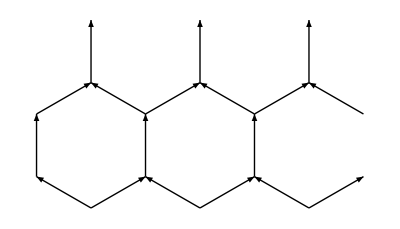

```mathematica
PlotArrays[lst_]:=Graphics[Table[Arrow[lst[[x]]],{x,Length[lst]}]];(*Я написал свою функцию PlotArrays для построения графика. Тут она объявляется *)
spins={
{{{1.73205,0.25},{1.73205,1.25}},{{1.73205,1.25},{0.866025,1.75}},{{0,1.25},{0.866025,1.75}},{{0,0.25},{0,1.25}},{{0.866025,-0.25},{0,0.25}},{{0.866025,-0.25},{1.73205,0.25}},{{3.4641,1.25},{2.59808,1.75}},{{1.73205,1.25},{2.59808,1.75}},{{2.59808,-0.25},{1.73205,0.25}},{{2.59808,-0.25},{3.4641,0.25}},{{0.866025,1.75},{0.866025,2.75}},{{2.59808,1.75},{2.59808,2.75}},{{5.19615,1.25},{4.33013,1.75}},{{3.4641,1.25},{4.33013,1.75}},{{3.4641,0.25},{3.4641,1.25}},{{4.33013,-0.25},{3.4641,0.25}},{{4.33013,-0.25},{5.19615,0.25}},{{4.33013,1.75},{4.33013,2.75}}}

};
fig1=PlotArrays[spins]
```

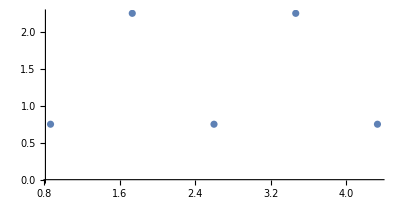

```mathematica
centers={
{{0.866025,0.75},{2.59808,0.75},{1.73205,2.25},{3.4641,2.25},{4.33013,0.75}}



};
fig2=ListPlot[centers,AspectRatio->1/2]
```

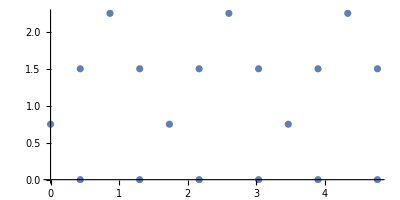

```mathematica
coord={
{{1.73205,0.75},{1.29904,1.5},{0.433013,1.5},{0,0.75},{0.433013,0},{1.29904,0},{3.03109,1.5},{2.16506,1.5},{2.16506,0},{3.03109,0},{0.866025,2.25},{2.59808,2.25},{4.76314,1.5},{3.89711,1.5},{3.4641,0.75},{3.89711,0},{4.76314,0},{4.33013,2.25}}



};

fig3=ListPlot[coord,AspectRatio->1/2]
```

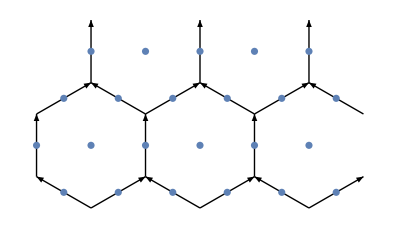

```mathematica
Show[fig1,fig2,fig3]
```

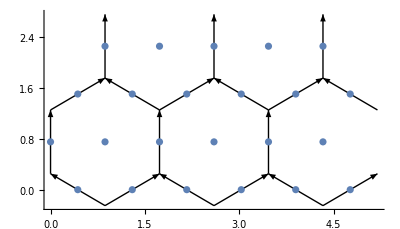

```mathematica
Show[%149,Axes->True,AxesStyle->Gray]
```

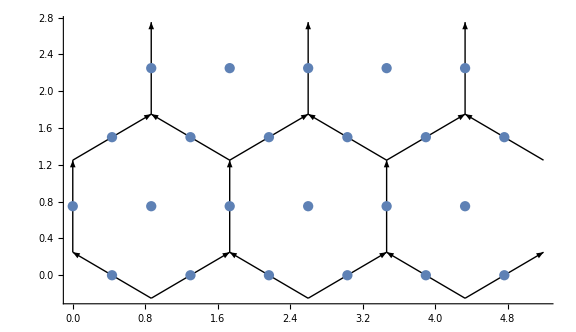

```mathematica
Show[%150,ImageSize->Large]
```